# Project 1 - Convolution

## Report

Emil Lengman, emillen@kth.se
Simon Enerstrand, simonene@kth.se

## Section. Summary INTE KLAR

For this project we had three sub-assignments. The three assignments built upon each other and are specified with

### Section.Subsection Summary sub-assignment 1

#### Description

This assignment is based on a dice game. There are five dice in the form of the Platonic solids (one die with 4 possible outcomes, one with 6, one with 8, one with 12, and one with 20). All dice are thrown at once, and if the sum of all dice are 10 or below, or 45 or higher, the player win a Teddy bear to bring home (each game costs 2 euro). We will:

Determine the exact probability function of the sum.

Determine the exact probability of winning the Teddy bear.

Determine the expected investment to win a Teddy.

Calculate the probability of winning at least once in twenty games.

#### Result

See section 2.1.

41/3840 . See section 2.2

187.317 euros. See section 2.3

0.193208. See Section 2.4

### Section.Subsection Summary sub-assignment 2

#### Description

This sub-assignment builds upon sub-assignment 1. Now are are playing for a car. The game has been modified to throw the five dice ten times, and if the sum of all dice S satisfies S≤200 or S≥350, you win a car. We will:

Determine the exact probability of winning the car.

Determine the expected investment to win a car.

#### Result

0.00118278

211366

### Section.Subsection Summary sub-assignment 3

#### Description

This assignment is based on a dice game. There are five dice in the form of the Platonic solids (one die with 4 possible outcomes, one with 6, one with 8, one with 12, and one with 20). All dice are thrown at once, and if the sum of all dice are 10 or below, or 45 or higher, the player win a Teddy bear to bring home (each game costs 2 euro). We will:

## Section. Winning a teddy

### Section.Subsection Probability function of the sum

#### Solution

To start off we defined the probability functions of the dice. Since the dice are perfect, all of the sides have the exact same probability of getting their face up, so we can define them as Discrete uniform distributions from 1 to the amount of faces the die has.

```mathematica
pf(k)=P(X=k)=Piecewise[{{1/m, 1≤k≤m}, {0, otherwise}}]
```

Then we performed Convolutions in order. First with die 1 and 2, then we took the result from that and convoluted it with die 3, and then 4 and lastly 5. This gave us the probability function of the sum.

#### Discussion

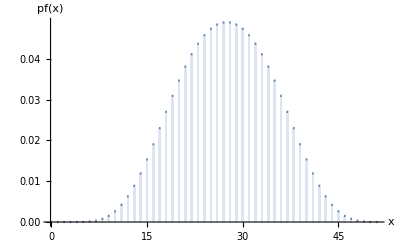

Above we have a diagram of the function

#### Code

```mathematica
ClearAll["`*"]
```

```mathematica
die1[x_] :=PDF[DiscreteUniformDistribution[{1, 4}],x]
die2[x_] :=PDF[DiscreteUniformDistribution[{1, 6}],x]
die3[x_] :=PDF[DiscreteUniformDistribution[{1, 8}],x]
die4[x_] :=PDF[DiscreteUniformDistribution[{1, 12}],x]
die5[x_] :=PDF[DiscreteUniformDistribution[{1, 20}],x]
```

```mathematica
pf1[s_]= pf1[s]=DiscreteConvolve[die1[y], die2[y], y, s];
pf2[s_]= pf2[s]=DiscreteConvolve[pf1[y], die3[y], y, s];
pf3[s_]= pf3[s]=DiscreteConvolve[pf2[y], die4[y], y, s];
pfResult[s_]= pfResult[s]=DiscreteConvolve[pf3[y], die5[y], y, s] ;(* pfResult is our function *)
```

```mathematica
Sum[pfResult[x], {x, 1, 50}] == 1
```

True

```mathematica
pfResult[5]
```

1/46080

```mathematica
pfResult[50]
```

1/46080

### Section.Subsection Exact probability to win Teddy

#### Solution

Now that we have the probability function of the sum of the dice, we can move on to calculate the probability of winning Teddy. We define the random variable S as the sum of the dice. We know that if S satisfies S≤10 or S≥45 you will win the Teddy. We can easily use that to calculate the probability.

```mathematica
P(X="winning teddy")= ∑_(k=5)^10 pf(k) +∑_(k=45)^50 pf(k)
```

We start at 5 because we know that it is the lowest possible outcome of the game, and stop at 50 because it is the highest.

#### Code

```mathematica
p = Sum[pfResult[x], {x, 5, 10}] + Sum[pfResult[x], {x, 45, 50}]
```

41/3840

### Section.Subsection Expected investment to win Teddy

#### Solution

To calculate the expected investment we need to to know how many times we are expected to play before winning. We know that calculating the expected value for a random variable that is distributed for finding the first successful event can be done like this.

```mathematica
μ= 1/p
```

Where p is the probability of  a successful outcome.

Now we only have to have to multiply the times we are expected to play with the cost (2 euros).

```mathematica
μ*2
```

#### Code

```mathematica
μ = N[(1 / p)*2] (* Smaller than in the explanation *)
```

187.317

### Section.Subsection Probability of winning Teddy in twenty games

#### Solution

We used binomial distribution to calculate the probability of winning Teddy after 20 games. We know that binomial distribution is used to calculate the probability of the random variable X which is defined as the amount of successful outcomes, while the probability of a successful outcome p, and the amount of tries n, is already defined.

```mathematica
pf(k)=P(X=k)=Piecewise[{{Binomial[n, k](p^k(1-p))^(n-k), 0≤k≤n}}]
```

#### Discussion

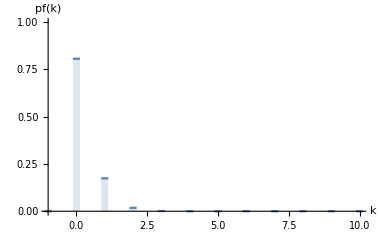

Here is a diagram of the binomial distribution function. It seems to coincide with our result (which is close 0.2). Here we can see that the chance of winning 0 times after 20 games is a little above 0.8.

#### Code

```mathematica
b := BinomialDistribution[20, p]
```

```mathematica
N[1 - PDF[b, 0]] (* The sum of all outcomes, subtracted by the chance of getting 0 wins *)
```

0.193208

## Section. Winning an electric car

### Section.Subsection Exact probability to win car

#### Solution

Here is a diagram of the binomial distribution function. It seems to coincide with our result (which is close 0.2). Here we can see that the chance of winning 0 times after 20 games is a little above 0.8.

#### Code INTE KLAR

```mathematica
ClearAll["`*"]
```

```mathematica
die1[x_] :=PDF[DiscreteUniformDistribution[{1, 4}],x]
die2[x_] :=PDF[DiscreteUniformDistribution[{1, 6}],x]
die3[x_] :=PDF[DiscreteUniformDistribution[{1, 8}],x]
die4[x_] :=PDF[DiscreteUniformDistribution[{1, 12}],x]
die5[x_] :=PDF[DiscreteUniformDistribution[{1, 20}],x]
```

```mathematica
pf1[s_]= pf1[s]=DiscreteConvolve[die1[y], die2[y], y, s];
pf2[s_]= pf2[s]=DiscreteConvolve[pf1[y], die3[y], y, s];
pf3[s_]= pf3[s]=DiscreteConvolve[pf2[y], die4[y], y, s];
pf4[s_]= pfResult[s]=DiscreteConvolve[pf3[y], die5[y], y, s] ;
```

```mathematica
KonvTable = Table[pf4[k], {k, 0, 50}];
KonvTable2 = ListConvolve[KonvTable, KonvTable, {1, -1}, 0];
KonvTable3 = ListConvolve[KonvTable2, KonvTable, {1, -1}, 0];
KonvTable4 = ListConvolve[KonvTable3, KonvTable, {1, -1}, 0];
KonvTable5 = ListConvolve[KonvTable4, KonvTable, {1, -1}, 0];
KonvTable6 = ListConvolve[KonvTable5, KonvTable, {1, -1}, 0];
KonvTable7 = ListConvolve[KonvTable6, KonvTable, {1, -1}, 0];
KonvTable8 = ListConvolve[KonvTable7, KonvTable, {1, -1}, 0];
KonvTable9 = ListConvolve[KonvTable8, KonvTable, {1, -1}, 0];
KonvTable10 = ListConvolve[KonvTable9, KonvTable, {1, -1}, 0];
```

```mathematica
p = 1;
```

### Section.Subsection Expected investment to win car

#### Solution

This is done the same way as in section 2.3. We used to following formula

```mathematica
μ= 1/p
```

Which is the expected amount of tries before winning.

Now we only have to have to multiply the times we are expected to play with the cost (250 euros).

```mathematica
μ*250
```

#### Code

```mathematica
N[(1/p)*250] (* Smaller than in the explanation *)
```

250.

## Section. Normal distribution

### Section.Subsection Expected investment to win car

#### Solution

### Section.Subsection Expected investment to win car

#### Solution

### Section.Subsection Comparison with section 2, and 3

#### Solution